```mathematica
Clear[ϵ]
```

```mathematica
(1/(50*365))/((1/(50*365))+1/7)
```

7/18257

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((-1+R)/10000+(√((-1+R)^2+4 p R))/10000)/(2 R)

```mathematica
ϵ=1/10000
```

1/10000

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→1/(10004000600040001 R^2)(-7998400080000 R+9000299950001 R^2-1000200010000 R^3-600 √1111 √(-99870049995000129999 R^2+299750038003799750003 R^3-299889986001400109997 R^4+100009997999800010001 R^5))},{p→1/(10004000600040001 R^2)(-7998400080000 R+9000299950001 R^2-1000200010000 R^3+600 √1111 √(-99870049995000129999 R^2+299750038003799750003 R^3-299889986001400109997 R^4+100009997999800010001 R^5))}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=1/(10004000600040001 R^2)(-7998400080000 R+9000299950001 R^2-1000200010000 R^3+600 √1111 √(-99870049995000129999 R^2+299750038003799750003 R^3-299889986001400109997 R^4+100009997999800010001 R^5))
```

```mathematica
h[R_]:=g[R+1]
```

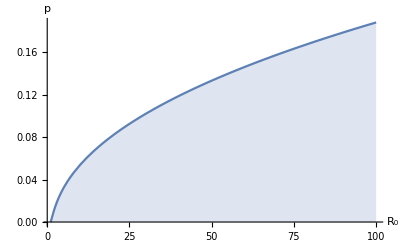

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

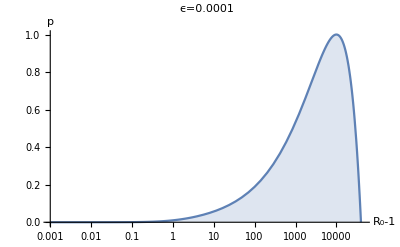

```mathematica
LogLinearPlot[h[R],{R,0.001,45000},Filling->Bottom,AxesLabel->{"R_0-1",p},PlotRange->{{0,45000},{0,1}},PlotLabel->"ϵ=0.0001"]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Documents\\GitHub\\RogerZhang\\July_6th\\Figures\\epsilon_0.0001.pdf",%25,"PDF"]
```

C:\Users\Roger Zhang\Documents\GitHub\RogerZhang\July_6th\Figures\epsilon_0.0001.pdf